```mathematica
1+1
```

2

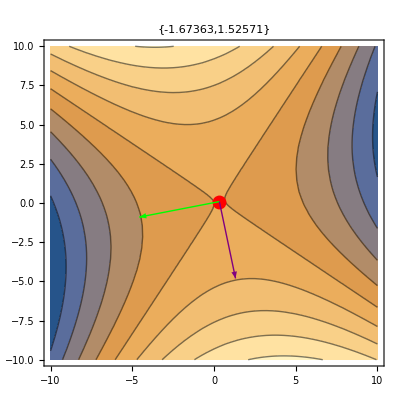

```mathematica
n=2;
A=RandomReal[{-1,1},{n,n}];
g=RandomReal[{-1,1},n];
A=A+Transpose[A];
x=LinearSolve[A,-g];
MatrixForm[A];
{{λ1,λ2},{v1,v2}}=Eigensystem[A];
ContourPlot[0.5*{x1,x2}.A.{x1,x2}+g.{x1,x2},{x1,-10,10},{x2,-10,10},
PlotLabel->{λ1,λ2},
Epilog->{
{Red, PointSize[.025],Point[x]},
{Green, Arrow[{x,x+5*v1}]},
{Purple,Arrow[{x,x+5*v2}]}
}]
```